## Temperature control with a nonlinear heater & gain scheduling (Ex. 11.2)

PI temperature control with nonlinearity from heater power:  P =V^2/R.

Null^2

NDSolveValue::ndsvb: There are multiple solution branches for the equations, but NDSolveValue will return only one. Use NDSolve to get all of the solution branches.

General::stop: Further output of NDSolveValue::ndsvb will be suppressed during this calculation.

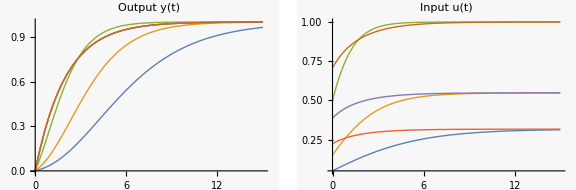

```mathematica
Clear["Global`*"];

tend=15;
values0={kp->1/2, ki->1/2} (* PI gains *);e[t]=r-y[t];  (* negative error term *)
(* naive PI control *)
eqs={y'[t]==- y[t]+ u[t]^2, u'[t]== ki e[t] - kp y'[t]}/.values0;
init={y[0]==0,u[0]==kp (r-y[0])}/.values0;

(* nonlinear PI control *)
eqs1={y'[t]==- y[t]+ u[t]^2, 2 u[t]u'[t]== ki e[t] - kp y'[t]}/.values0;
init1={y[0]==0,u[0]^2==kp (r-y[0])}/.values0;

rlist={0.1,0.3,1}; rsize=Length[rlist];
solA=Table[NDSolveValue[{eqs,init}/.r->r0,{y,u},{t,0,tend}],{r0,rlist}];
solB=Table[NDSolveValue[{eqs1,init1}/.r->r0,{y,u},{t,0,tend}],{r0,rlist}];
yA=solA[[All,1]]; yB=solB[[All,1]]; uA=solA[[All,2]]; uB=solB[[All,2]];

py=Plot[Evaluate[{Table[(yA[[i]][t])/rlist[[i]],{i,rsize}],Table[(yB[[i]][t])/rlist[[i]],{i,3}]}],{t,0,tend},PlotLabel->"Output y(t)",PlotRange->All,PlotStyle->{Thick},ImagePadding->{{25,5},{15,5}}];
pu=Plot[Evaluate[{Table[uA[[i]][t],{i,rsize}],Table[Abs[uB[[i]][t]],{i,3}]}],{t,0,tend},PlotLabel->"Input u(t)",PlotRange->All,PlotStyle->{Thick},ImagePadding->{{25,5},{15,5}}];
GraphicsRow[{py,pu},ImageSize->Large]
```

Export data

```mathematica
dt=0.01;
ydat=Table[{yA[[i]][t],yB[[i]][t]},{t,0,tend,dt},{i,rsize}];
ydat1=Partition[Flatten[ydat],2rsize];  (* reshape to have 2d array, 2*rlist elements across *)
(*
SetDirectory[NotebookDirectory[]];
Export["yDat1.dat",ydat1];
*)
```

In a similar spirit, we could explore how to compensate for a nonlinearity at the INPUT.  In particular, the temperature sensor  (thermistor) obeys the (inverse) Steinhart-Hart formula.  Its response can be made more nearly linear by placing into a voltage divider.

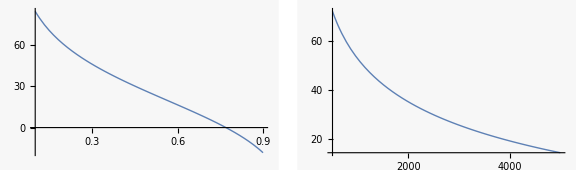

```mathematica
r[v_]:=v/(1-v)rref/.rref->3000;    (* r = thermistor resistance divided by reference resistance in voltage divider; 
similarly, v = (voltage out / voltage in) for voltage divider circuit *)
T[r_]:=1/(a+b x+c x^3)-273.15//.{x->Log[r],a->1.4 10^-3,b->2.37 10^-4,c->9.9 10^-8}
ptv=Plot[T[r[v]],{v,0.1,0.9},ImagePadding->{{25,10},{15,5}}];ptr=Plot[T[r],{r,500,5000},ImagePadding->{{25,10},{15,5}}];
GraphicsRow[{ptv,ptr},ImageSize->Large]
```

Notice how the temperature-voltage relation at left (in the configuration of a voltage divider) is more linear than the basic thermistor relation (right).  The temperature sensitivity (∂_V T)is thus more nearly equal across a wider range, which helps maintain signal-to-noise ratios (see also Chapter 15, Section 2).  Since we did not pursue this generalization in the book, it is an exercise to the reader to incorporate the nonlinear T[v] relation into a controller....